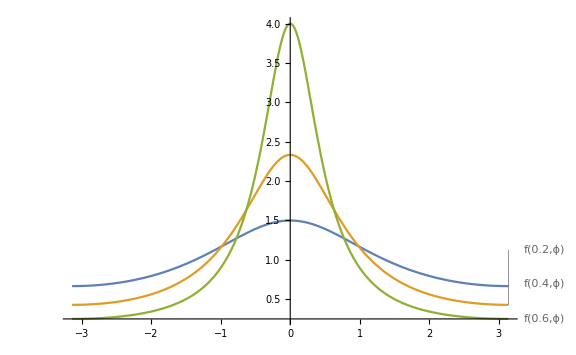
{-Graphics3D-,-Graphics-}

```mathematica
f[r_, ϕ_] := (1-r^2)/(1-2*r*Cos[ϕ]+r^2)
{Plot3D[f[r,ϕ],{r,0,1},{ϕ,-π,π},PlotRange->Automatic,ImageSize->Medium],Plot[{f[0.2,ϕ],f[0.4,ϕ],f[0.6,ϕ]},{ϕ,-π,π},PlotLabels->Automatic,ImageSize->Large]}
```